Setup movement

The rows are all CSV rows, which are x, y, z, label, ...; we want just the first three, which are acceleration in 10ms^-2

```mathematica
fn="sbbc-1.csv";
rows = Import[FileNameJoin[{NotebookDirectory[], fn}]];
rowCount = Length[rows];
```

The file contains a lot of rows, so we want to select just a subset of about 20k samples

```mathematica
rowsSubset=rows[[1;;1500,All]]; 
acceleration=Transpose[rowsSubset[[All,1;;3]]];
acceleration=Map[LowpassFilter[#,.1]&,acceleration];
normalize=Identity;
acceleration=normalize/@ acceleration;
labelFunction[x_]:=If[x=="exercising",-1,1];
labels=Map[labelFunction,rowsSubset[[All,4]]];
```

Finally, we display the data

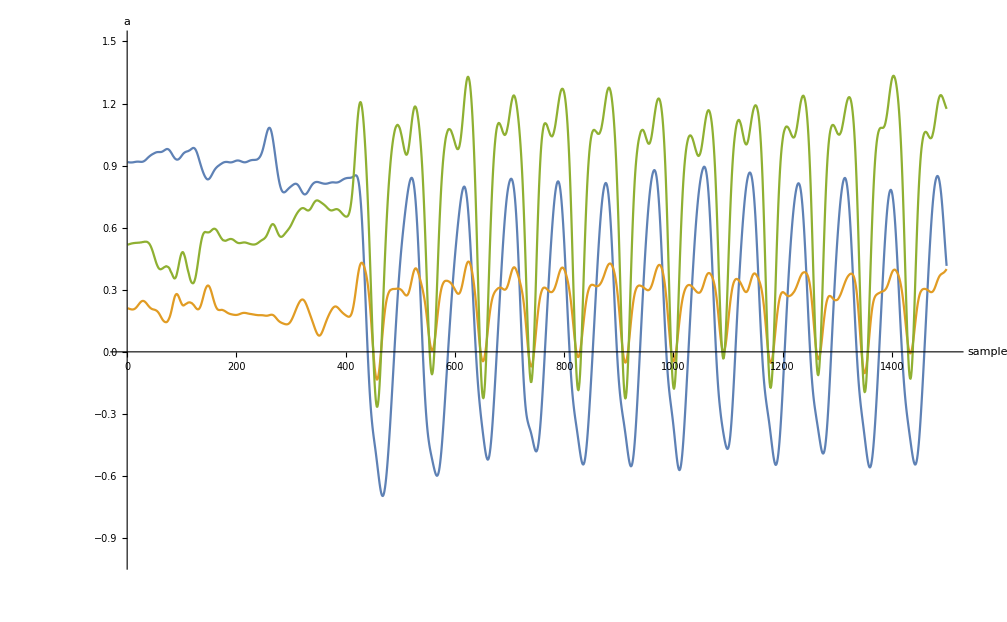

```mathematica
ListLinePlot[acceleration,{TargetUnits->{"sample","a"},AxesLabel->Automatic,PlotRange->{-1,1.5}}]
```

Suppose there are gaps, let’s see if we can predict the missing values